## EdgeBetween example

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51a (07 June 2017)) loaded Wed 7 Jun 2017 14:49:27
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

```mathematica
T=TemplateRandomSquareGrid[15, {0,0}, {15, 5}];
```

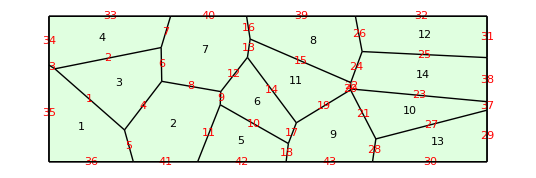

```mathematica
ShowTissue[T, "CellNumbers"-> True, "EdgeNumbers"-> True,  "EdgeNumberStyle"-> {Red,Background-> Yellow}]
```

```mathematica
EdgeBetween[T,2,4]
```

{}

```mathematica
EdgeBetween[T,2,3]
```

4

## Make a matrix of edge numbers entry M[i,j] --> gives edge between cell i and cell j, or {}

```mathematica
M={};
For[i=1,i≤14,i = i+1,
row={};
For[j=1,j≤14,j=j+1,
AppendTo[row,EdgeBetween[T,i,j]]
]
AppendTo[M,row]
]
MatrixForm[M]
```

({} | 5 | 1 | 3 | {} | {} | {} | {} | {} | {} | {} | {} | {} | {}
5 | {} | 4 | {} | 11 | 9 | 8 | {} | {} | {} | {} | {} | {} | {}
1 | 4 | {} | 2 | {} | {} | 6 | {} | {} | {} | {} | {} | {} | {}
3 | {} | 2 | {} | {} | {} | 7 | {} | {} | {} | {} | {} | {} | {}
{} | 11 | {} | {} | {} | 10 | {} | {} | 18 | {} | {} | {} | {} | {}
{} | 9 | {} | {} | 10 | {} | 12 | {} | 17 | {} | 14 | {} | {} | {}
{} | 8 | 6 | 7 | {} | 12 | {} | 16 | {} | {} | 13 | {} | {} | {}
{} | {} | {} | {} | {} | {} | 16 | {} | {} | {} | 15 | 26 | {} | 24
{} | {} | {} | {} | 18 | 17 | {} | {} | {} | 21 | 19 | {} | 28 | {}
{} | {} | {} | {} | {} | {} | {} | {} | 21 | {} | 20 | {} | 27 | 23
{} | {} | {} | {} | {} | 14 | 13 | 15 | 19 | 20 | {} | {} | {} | 22
{} | {} | {} | {} | {} | {} | {} | 26 | {} | {} | {} | {} | {} | 25
{} | {} | {} | {} | {} | {} | {} | {} | 28 | 27 | {} | {} | {} | {}
{} | {} | {} | {} | {} | {} | {} | 24 | {} | 23 | 22 | 25 | {} | {})

```mathematica
EdgeBetween[T, 3,3]
```

{}